Se presenta gráficas de los índices de refracción de datos experimentales obtenidos de https://refractiveindex.info/ para diversos materiales

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

```mathematica
Needs["MaTeX`"]
```

### Oro

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en um*)
ℏωAu=h c/λAu; (*eV*)
nau=nau1[[All,2]];
kAu=kau1[[All,2]];
nAu=nau+ I kAu;
```

```mathematica
hbarraomegaAu=Drop[ℏωAu,{1,2}];
epsReal=Re[Drop[nAu,{1,2}]^2];
epsImag=Im[Drop[nAu,{1,2}]^2];
```

```mathematica
auReal = Interpolation[Transpose[{hbarraomegaAu,epsReal}]];
auImag = Interpolation[Transpose[{hbarraomegaAu,epsImag}]];
```

```mathematica
nAu[[1]]^2
epsReal[[1]]
epsImag[[1]]
```

0.227056+3.04128 ⅈ

0.227056

3.04128

```mathematica
h c/2.5
```

496.28

```mathematica
upperTicks4=Module[{labels,positions},labels={310,355,414,496,620,827,1240};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

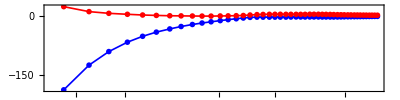

```mathematica
drudeAu=ListLogLinearPlot[{Style[auReal ,Blue],Style[auImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],PlotMarkers->{•},Joined->True,PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],None}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,None}},PlotRange->All,AspectRatio->1/4]
```

```mathematica
Export["drudeAu.svg",drudeAu]
```

drudeAu.svg

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en um*)
ℏωAg=h c/λAg; (*eV*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

```mathematica
hbarraomegaAg0=Drop[ℏωAg,{1,20}];
hbarraomegaAg=Drop[hbarraomegaAg0,{-13,-1}];
nAggg=Drop[nAgg,{1,20}];
epsRealAg=Re[Drop[nAggg,{-13,-1}]^2];
epsImagAg=Im[Drop[nAggg,{-13,-1}]^2];
```

```mathematica
hbarraomegaAg
```

{4.1233,3.99324,3.87235,3.74269,3.62248,3.50282,3.37238,3.25216,3.12204,3.00194,2.882,2.75161,2.63195,2.50192,2.38184,2.26158}

```mathematica
agReal = Transpose[{hbarraomegaAg,epsRealAg}];
agImag = Transpose[{hbarraomegaAg,epsImagAg}];
```

```mathematica
h c/2.5
```

496.28

```mathematica
upperTicks4=Module[{labels,positions},labels={310,355,414,496,620,827,1240};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

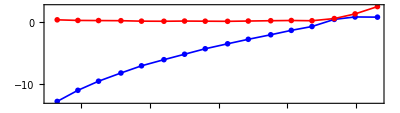

```mathematica
drudeAg=ListPlot[{Style[agReal ,Blue],Style[agImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],PlotMarkers->{•},Joined->True,PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],None}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,None}},PlotRange->All,AspectRatio->1/3.5]
```

```mathematica
Export["drudeAg.svg",drudeAg]
```

drudeAg.svg

### Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
bism=Import["C:\\Users\\Lunita\\OneDrive\\Documentos\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]]*100;(*λ en um*)
ℏωBism=h c/λBism; (*eV*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

```mathematica
hbarraomegaBi=Drop[Drop[ℏωBism,{1,136}],{14}];
epsRealBi=Drop[Re[Drop[nBismuto,{1,136}]^2],{14}];
epsImagBi=Drop[Im[Drop[nBismuto,{1,136}]^2],{14}];
```

```mathematica
biReal = Interpolation[Transpose[{hbarraomegaBi,epsRealBi}]];
biImag = Interpolation[Transpose[{hbarraomegaBi,epsImagBi}]];
```

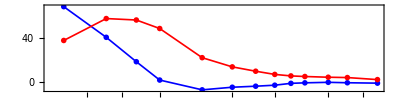

```mathematica
drudeBi=ListLogLinearPlot[{Style[biReal ,Blue],Style[biImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],PlotMarkers->{•},Joined->True,PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],None}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,None}},PlotRange->All,AspectRatio->1/4]
```

```mathematica
Export["drudeBi.svg",drudeBi]
```

drudeBi.svg

```mathematica
h c/(5*10^(8))
```

2.4814×10^-6

```mathematica
upperTicks4=Module[{labels,positions},labels={2.5*^-6,3.1*^-6,4.1*^-6,6.2*^-6,1.24*10^(-5)};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

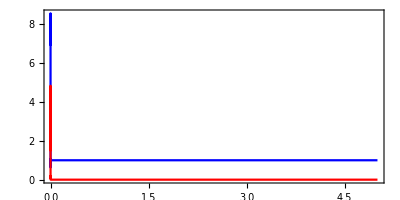

```mathematica
bis=ListLinePlot[{Style[Transpose[{ℏωBism,nBis}],Blue],Style[Transpose[{ℏωBism,kBis}],Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["n,k"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["n"],MaTeX["k "]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}],AspectRatio->1/2]
```

```mathematica
Export["Bisexp.svg",bis]
```

Bisexp.svg

### Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]]*1000;(*λ en um*)
ℏωMgO=2 Pi c ℏ/λMgO; (*eV*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

```mathematica
hbarraomegaMgO=Drop[ℏωMgO,{-95,-1}];
epsRealMgO=Re[Drop[nMgO,{-95,-1}]^2];
epsImagMgO=Im[Drop[nMgO,{-95,-1}]^2];
```

```mathematica
mgOReal = Interpolation[Transpose[{hbarraomegaMgO,epsRealMgO}]];
mgOImag = Interpolation[Transpose[{hbarraomegaMgO,epsImagMgO}]];
```

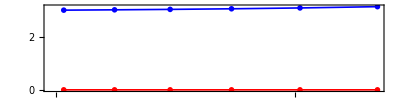

```mathematica
drudeMgO=ListLogLinearPlot[{Style[mgOReal ,Blue],Style[mgOImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],PlotMarkers->{•},Joined->True,PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],None}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,None}},PlotRange->All,AspectRatio->1/4]
```

```mathematica
Export["drudeMgO.svg",drudeMgO]
```

drudeMgO.svg

### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]];
ℏωalum=2 Pi c ℏ/λalum; (*eV*)
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
```

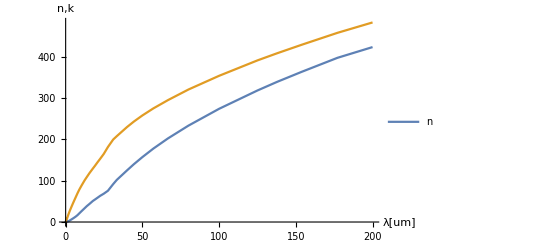

```mathematica
ListLinePlot[{Transpose[{λalum,nalum}],Transpose[{λalum,kalum}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n"}]
```

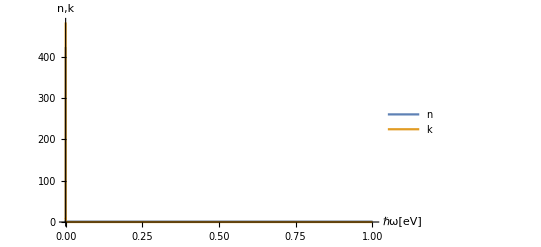

```mathematica
ListLinePlot[{Transpose[{ℏωalum,nalum}],Transpose[{ℏωalum,kalum}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n,k"},PlotLegends->{"n","k"}]
```

```mathematica
h c/350
```

3.54486

```mathematica
ϵℏω[ℏω_,ℏωp_,ℏγ_]:=1-((ℏωp/ℏ)^2/((ℏω/ℏ)((ℏω/ℏ)+ I * (ℏγ/ℏ))))(*recibe en eV*)
```

```mathematica
alReal=Table[{ℏω,Re[ϵℏω[ℏω,13.142,0.197]]},{ℏω,3.5448580251428568,9.9256024704,0.01}];
alImag=Table[{ℏω,Im[ϵℏω[ℏω,13.142,0.197]]},{ℏω,3.5448580251428568,9.9256024704,0.01}];
```

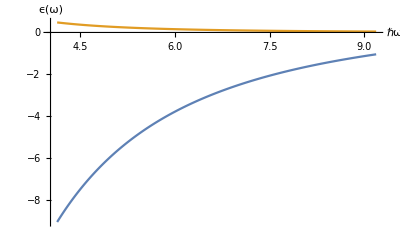

```mathematica
ListLinePlot[{alReal,alImag},AxesLabel->{"ℏω","ϵ(ω)"}]
```

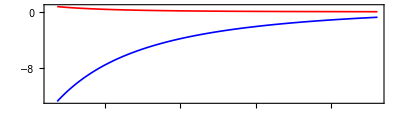

```mathematica
drudeAl=ListPlot[{Style[alReal ,Blue],Style[alImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],Joined->True,PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],None}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,None}},PlotRange->All,AspectRatio->1/3.5]
```

```mathematica
Export["drudeAl.svg",drudeAl]
```

drudeAl.svg